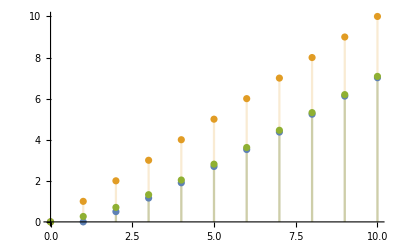

```mathematica
DiscretePlot[{Log[4,CatalanNumber[n]],Log[4,4^n],Log[4,4^n/(1+n^(3/2)Sqrt[Pi])]},{n,0,10}]
```

```mathematica
runs[l_]:=Split[l,#1+1==#2&];
runLengths[l_]:=Length/@runs[l];
isolatedMatchings[l_]:=Times@@(CatalanNumber/@runLengths[l]);
i4[l_]:=Times@@(c4/@runLengths[l])
```

```mathematica
b[n_]:=
With[
{m=n/2-1},
CatalanNumber[m/2+1]^2Sum[CatalanNumber[i-1]CatalanNumber[m/2+1-i],{i,1,m/2+1}]^2]
```

```mathematica
c4[n_]:=4^n
```

```mathematica
b4[n_]:=
With[
{m=n/2-1},
c4[m/2+1]^2Sum[c4[i-1]c4[m/2+1-i],{i,1,m/2+1}]^2]
```

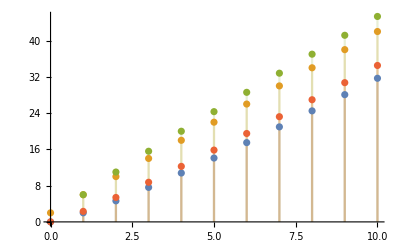

```mathematica
DiscretePlot[{Log[4,b[4μ+2]],Log[4,4^(4μ+2)],Log[4,b4[4μ+2]],Log[4,CatalanNumber[(4μ+2)/2]^2]},{μ,0,10}]
```

```mathematica
Limit[Log[4,b4[n]]/n,n->∞]
```

1

```mathematica
bound[n_,γ_]:=
With[
{m=n/2-γ},
CatalanNumber[m/2+γ]^2Total[isolatedMatchings/@Subsets[Range[m/2+γ],{m/2}]]^2]
```

```mathematica
bound4[n_,γ_]:=
With[
{m=n/2-γ},
c4[m/2+γ]^2Total[i4/@Subsets[Range[m/2+γ],{m/2}]]^2]
```

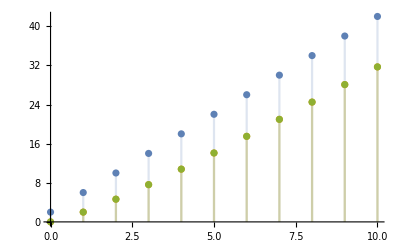

```mathematica
DiscretePlot[{Log[4,4^(4μ+2)],Log[4,b[4μ+2]],Log[4,bound[4μ+2,1]]},{μ,0,10}]
```

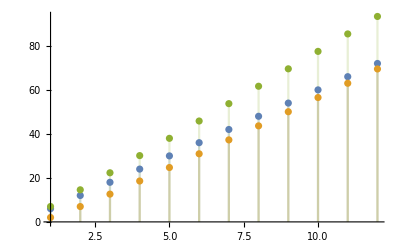

```mathematica
DiscretePlot[{Log[4,4^(4μ+2μ)],Log[4,bound[4μ+2μ,μ]],Log[4,bound4[4μ+2μ,μ]]},{μ,1,12}]
```

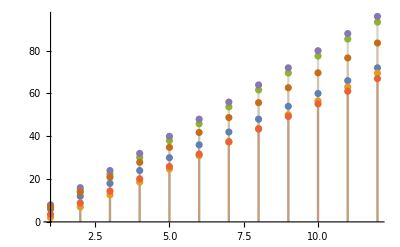

```mathematica
DiscretePlot[{Log[4,4^(4μ+2μ)],Log[4,bound[4μ+2μ,μ]],Log[4,bound4[4μ+2μ,μ]],Log[4,CatalanNumber[4μ+2μ]],Log[4,4^(8μ)],Log[4,5^(4μ+2μ)]},{μ,1,12}]
```

```mathematica
Table[CatalanNumber[2n]-CatalanNumber[n]^2,{n,1,10}]
```

{1,10,107,1234,15032,190588,2490399,33312770,453999656,6282014804}

```mathematica
Table[4^(2n)-CatalanNumber[2n],{n,1,10}]
```

{14,242,3964,64106,1031780,16569204,265761016,4259609626,68241838036,1092947507356}

```mathematica
spcDirectkEq2l=Table[With[{k=2l},Total[isolatedMatchings/@Subsets[Range[k],{l}]]],{l,1,8}]
```

{2,9,48,275,1638,9996,62016,389367}

```mathematica
spcDirectkEq2l=Table[With[{k=2l},Sum[Product[CatalanNumber[ρ],{ρ,runLengths[S]}],{S,Subsets[Range[k],{l}]}]],{l,1,8}]
```

{2,9,48,275,1638,9996,62016,389367}

```mathematica
spcDirectkEq3l=Table[With[{k=3l},Sum[Product[CatalanNumber[ρ],{ρ,runLengths[S]}],{S,Subsets[Range[k],{l}]}]],{l,1,5}]
```

{3,20,154,1260,10659}

```mathematica
Clear[spc];
spc[k_,k_]:=CatalanNumber[k];
spc[k_,l_]:=spc[k,l]=Sum[spc[k-i,k-i-((k-l)-1)]CatalanNumber[i-1],{i,1,l+1}]
```

```mathematica
k-i-((k-l)-1)
```

1-i+l

```mathematica
Table[spc[2l,l],{l,1,8}]
```

{2,9,48,275,1638,9996,62016,389367}

```mathematica
Table[spc[3l,l],{l,1,5}]
```

{3,20,154,1260,10659}

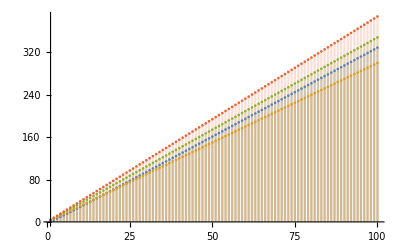

```mathematica
DiscretePlot[{Log[4,CatalanNumber[2l]spc[2l,l]],Log[4,4^(3l)],Log[4,5^(3l)],Log[4,6^(3l)]},{l,1,100}]
```

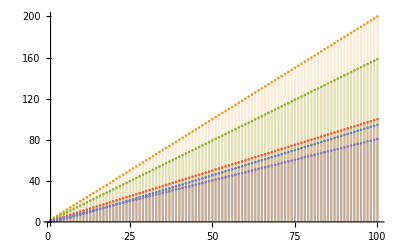

```mathematica
DiscretePlot[{Log[4,spc[l,l]],Log[4,4^(2l)],Log[4,3^(2l)],Log[4,2^(2l)],Log[4,1.75^(2l)]},{l,1,100}]
```

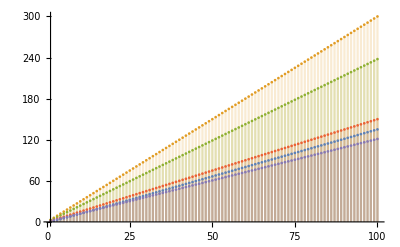

```mathematica
DiscretePlot[{Log[4,spc[2l,l]],Log[4,4^(3l)],Log[4,3^(3l)],Log[4,2^(3l)],Log[4,1.75^(3l)]},{l,1,100}]
```

```mathematica
6^(1/3)*4^(2/3)//N
```

4.57886

```mathematica
k-i-((k-l)-1)
```

1-i+l

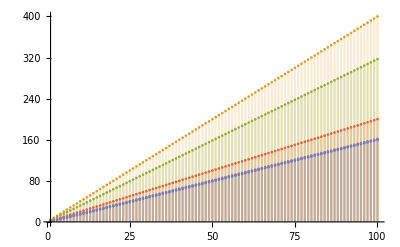

```mathematica
DiscretePlot[{Log[4,spc[3l,l]],Log[4,4^(4l)],Log[4,3^(4l)],Log[4,2^(4l)],Log[4,1.75^(4l)]},{l,1,100}]
```

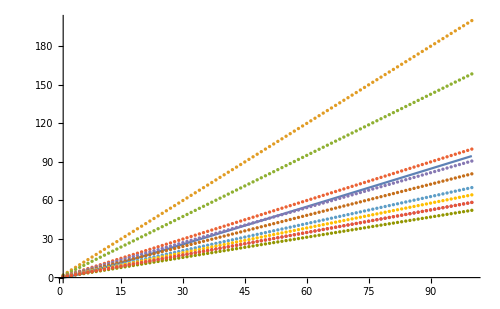
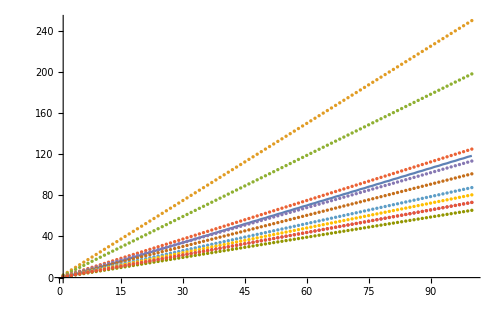
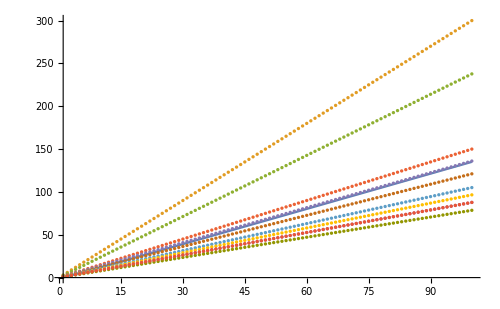
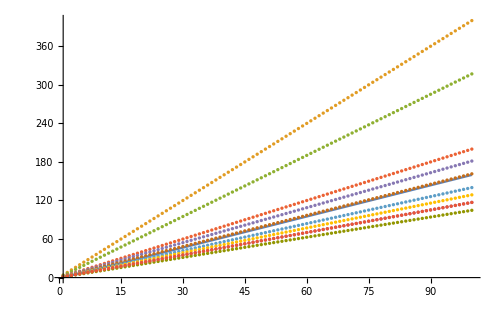
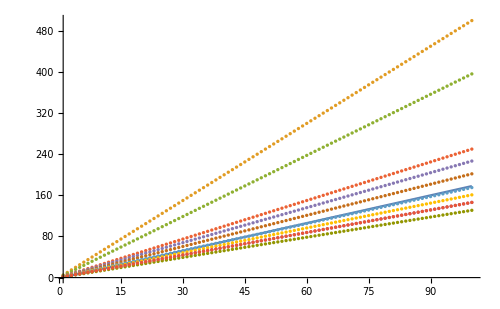
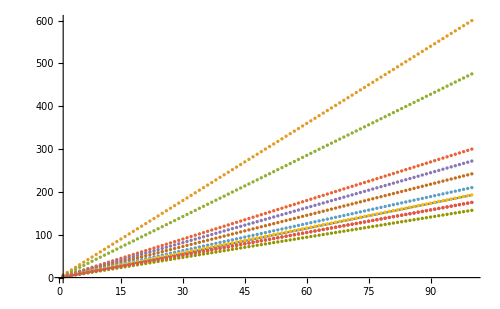
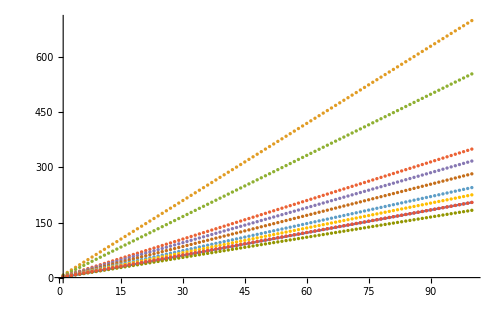
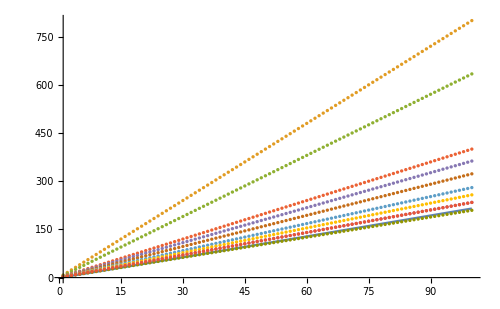
1
-Graphics- | 1.5
-Graphics- | 2
-Graphics-
3
-Graphics- | 4
-Graphics- | 5
-Graphics-
6
-Graphics- | 7
-Graphics- | 8
-Graphics-

```mathematica
Partition[
Table[
{λ,DiscretePlot[{Log[4,spc[Ceiling[λ l],l]],Log[4,4^((λ+1)l)],Log[4,3^((λ+1)l)],Log[4,2^((λ+1)l)],Log[4,(2-1/8)^((λ+1)l)],Log[4,1.75^((λ+1)l)],Log[4,(2-1/4-1/8)^((λ+1)l)],Log[4,(2-1/4-1/8-1/16)^((λ+1)l)],Log[4,(2-1/4-1/8-2/16)^((λ+1)l)],Log[4,(2-1/4-1/8-3/16)^((λ+1)l)],Log[4,(1.5)^((λ+1)l)]},{l,1,100},ImageSize->500,Filling->None,Joined->{True,False,False,False,False,False,False,False,False,False,False,False}]},
{λ,{1,1.5,2,3,4,5,6,7,8}}],3]//TableForm
```

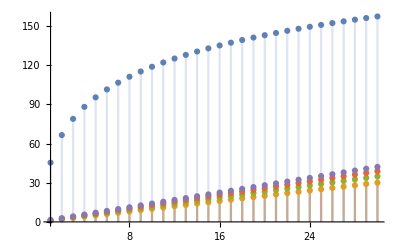

```mathematica
With[{l=50},DiscretePlot[{Log[4,spc[p l,l]],Log[4,4^(p)],Log[4,5^(p)],Log[4,6^(p)],Log[4,7^(p)]},{p,1,30}]]
```

```mathematica
k-i+(k-i-((k-l)-1))/.i->j+1//Simplify
```

-1-2 j+k+l